```mathematica
ClearAll["Global`*"]
```

0.25

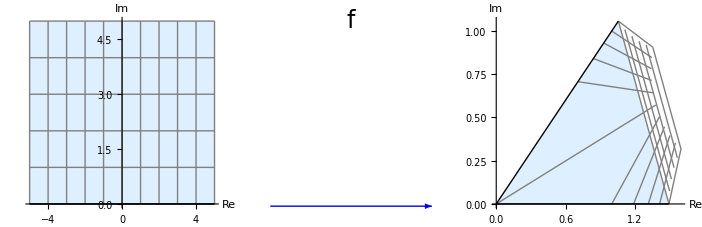

```mathematica
f[z_,a_]:=z^a

(*Set the transformation parameter a between 0 and 2*)
a=0.25

(*Create grid lines for the original z-plane region*)
xRange={-5,5};
yRange={0,5};
gridSpacingX=1;
gridSpacingY=1;

(*Define grid lines in the upper half-plane of z*)
gridLinesZ=Flatten[{Table[Line[{{x,0},{x,yRange[[2]]}}],{x,xRange[[1]],xRange[[2]],gridSpacingX}],Table[Line[{{xRange[[1]],y},{xRange[[2]],y}}],{y,yRange[[1]],yRange[[2]],gridSpacingY}]},1];

(*Plot the original z-plane with grid lines*)
originalRegion=Graphics[{LightBlue,Rectangle[{xRange[[1]],yRange[[1]]},{xRange[[2]],yRange[[2]]}],Gray,gridLinesZ,Black,Line[{{xRange[[1]],0},{xRange[[2]],0}}]  (*x-axis*)},Axes->True,AxesOrigin->{0,0},PlotRange->{{xRange[[1]],xRange[[2]]},{yRange[[1]],yRange[[2]]}},AxesLabel->{"Re","Im"}];

(*Transform grid lines*)
transformedGridLinesZ=gridLinesZ/. Line[pts_]:>Line[ReIm/@(f[#,a]&/@(pts[[All,1]]+I pts[[All,2]]))];

(*Define the endpoints of the transformed boundary lines*)
v1=ReIm[f[xRange[[1]],a]];
v2=ReIm[f[xRange[[2]],a]];

(*Plot the transformed w-plane with extended blue coloring and boundaries*)
transformedRegion=Graphics[{LightBlue,Polygon[{{0,0},v1,v2}],(*The sector*)Gray,transformedGridLinesZ,Black,Line[{{0,0},v1}],(*Boundary line 1*)Black,Line[{{0,0},v2}]   (*Boundary line 2*)},Axes->True,AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"Re","Im"},ImagePadding->{{50,Automatic},{30,30}}];

(*Define an arrow graphic with the label'f'*)arrowGraphic=Graphics[{Blue,Arrowheads[0.05],Arrow[{{0,0},{0.25,0}}],Black,Text[Style["f",FontSize->24],{0.125,0.05}]},ImageSize->Small  (*Adjust the size to fit between the plots*), ImagePadding->{{Automatic,Automatic},{30,40}}];

(*Combine the original region,arrow graphic,and transformed region in a row*)
fullGraphic=GraphicsRow[{originalRegion,arrowGraphic,transformedRegion},Spacings->{Scaled[0.1],Scaled[0.5]},ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}}  (*Increase padding at the top and bottom*)];

(*Display the full graphic*)
fullGraphic
```